```mathematica
BD= a Ν P/ (1 + a h Ν + γ (P-1));
dBD=D[BD,γ]
```

-(a (-1+P) P Ν)/(1+(-1+P) γ+a h Ν)^2

```mathematica
AA=a Ν P/ (P^m+ a h Ν);
dAA=D[AA,m]
```

-(a P^(1+m) Ν Log[P])/((P^m+a h Ν)^2)

```mathematica
(* Set γ as function of m so that strength of interference is equal in BD and AA models *)Solve[P^m== γ P,γ]
```

{{γ→P^(-1+m)}}

```mathematica
parms = {m-> 0.5, P-> 3,a-> 1, h-> 2, Ν-> 2};
parms=Join[{γ -> P^(m-1)/.parms},parms]
```

{γ→0.57735,m→0.5,P→3,a→1,h→2,Ν→2}

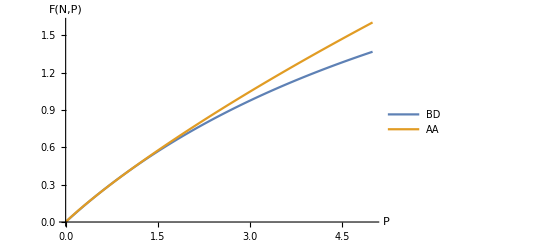

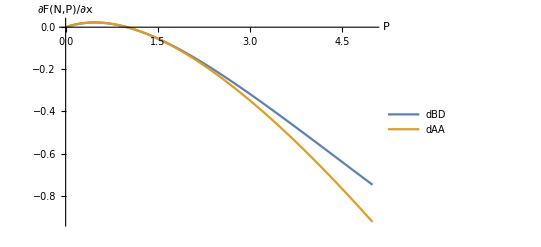

```mathematica
(* Plot prey count as function of P *)Plot[{BD/.Drop[parms,{3}], AA/.Drop[parms,{3}]},{P,0,5},PlotLegends->{"BD","AA"},AxesLabel->{"P","F(N,P)"}]
(* Plot sensitivity of prey count wrt to interference as function of P *)
Plot[{dBD/.Drop[parms,{3}], dAA/.Drop[parms,{3}]},{P,0,5},PlotLegends->{"dBD","dAA"},AxesLabel->{"P","∂F(N,P)/∂x"}]
```

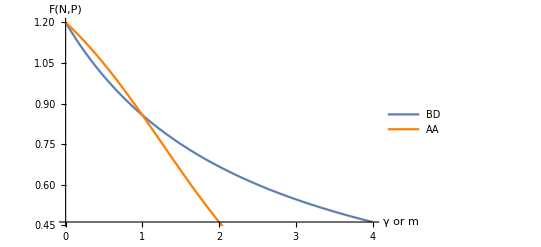

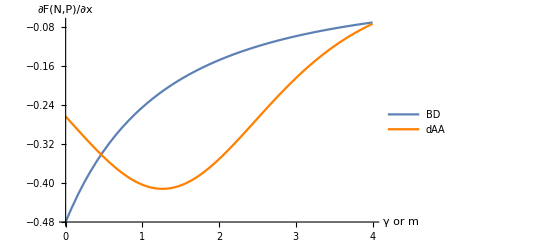

```mathematica
(* Plot prey count as function of interference *)P1=Plot[BD/.Drop[parms,{1}],{γ,0,4},PlotLegends->{"BD"},AxesLabel->{"γ or m","F(N,P)"}];
P2=Plot[AA/.Drop[parms,{2}],{m,0,4},PlotLegends->{"AA"},PlotStyle-> Orange];
Show[P1,P2]
(* Plot sensitivity of prey count wrt to interference as function of interference *)
P1=Plot[dBD/.Drop[parms,{1}],{γ,0,4},PlotLegends->{"BD"},AxesLabel->{"γ or m","∂F(N,P)/∂x"}];
P2=Plot[dAA/.Drop[parms,{2}],{m,0,4},PlotLegends->{"dAA"},PlotStyle-> Orange,AxesLabel->{"P","∂F(N,P)/∂x"}];
Show[P1,P2]
```

```mathematica
Manipulate[
parms = {m-> μ, P-> Π,a-> α, h-> η, Ν-> ν};
parms=Join[{γ -> P^(m-1)/.parms},parms];
Grid[{{
(* Plot prey count as function of P *)Plot[{BD/.Drop[parms,{3}], AA/.Drop[parms,{3}]},{P,0,5},AxesLabel->{"P","F(N,P)"}]
,
(* Plot sensitivity of prey count wrt to interference as function of P *)
Plot[{dBD/.Drop[parms,{3}], dAA/.Drop[parms,{3}]},{P,0,5},AxesLabel->{"P","∂F(N,P)/∂x"}]
},{
(* Plot prey count as function of interference *)P1=Plot[BD/.Drop[parms,{1}],{γ,0,4},AxesLabel->{"γ or m","F(N,P)"}];
P2=Plot[AA/.Drop[parms,{2}],{m,0,4},PlotStyle-> Orange];
Show[P1,P2]
,
(* Plot sensitivity of prey count wrt to interference as function of interference *)
P1=Plot[dBD/.Drop[parms,{1}],{γ,0,4},AxesLabel->{"γ or m","∂F(N,P)/∂x"}];
P2=Plot[dAA/.Drop[parms,{2}],{m,0,4},PlotStyle-> Orange,AxesLabel->{"P","∂F(N,P)/∂x"}];
Show[P1,P2],
parms
}}],
{{μ,0.5,"m"},0,2},
{{Π,3,"P"},1,10},
{{α,1,"a"},0,2},
{{η,2,"h"},0,4},
{{ν,2,"Ν"},0,20}
]
```